```mathematica
SetOptions[Plot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[LogPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[LogLogPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[LogLinearPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[ListPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[DiscretePlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];SetOptions[ListLogPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[ListLogLogPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[BarChart,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
```

```mathematica
cl=Directive/@ColorData[97,"ColorList"]
```

{Directive[RGBColor[0.368417, 0.506779, 0.709798]],Directive[RGBColor[0.880722, 0.611041, 0.142051]],Directive[RGBColor[0.560181, 0.691569, 0.194885]],Directive[RGBColor[0.922526, 0.385626, 0.209179]],Directive[RGBColor[0.528488, 0.470624, 0.701351]],Directive[RGBColor[0.772079, 0.431554, 0.102387]],Directive[RGBColor[0.363898, 0.618501, 0.782349]],Directive[RGBColor[1, 0.75, 0]],Directive[RGBColor[0.647624, 0.37816, 0.614037]],Directive[RGBColor[0.571589, 0.586483, 0.]],Directive[RGBColor[0.915, 0.3325, 0.2125]],Directive[RGBColor[0.40082222609352647, 0.5220066643438841, 0.85]],Directive[RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142]],Directive[RGBColor[0.736782672705901, 0.358, 0.5030266573755369]],Directive[RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]]}

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\sgros\Google Drive\students\Sam PhD\presentation

## Bouchaud and Mezard

```mathematica
p[m_,w_]=Exp[-(m-1)/w]/w^(1+m)*(m-1)^m/Gamma[m]
```

(ⅇ^((1-m)/w) (-1+m)^m w^(-1-m))/Gamma[m]

```mathematica
ptail[m_,x_]=1-Integrate[p[m,w],{w,0,x},Assumptions->x>0&&m>1]
```

1-Gamma[m,(-1+m)/x]/Gamma[m]

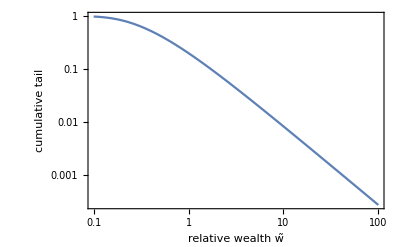

```mathematica
LogLogPlot[ptail[1.5,w],{w,0.1,100},FrameLabel->{"relative wealth w̃","cumulative tail"}]
```

## Mixture of Exponential Distributions

```mathematica
PDF[GammaDistribution[α,β],x]
```

Piecewise[{{(ⅇ^(-x/β) x^(-1+α) β^-α)/Gamma[α], x>0}, {0, True}}]

```mathematica
Mean[GammaDistribution[α,β]]
StandardDeviation[GammaDistribution[α,β]]
```

α β

√α β

```mathematica
mix[x_,α_,β_]=FullSimplify[Integrate[l*Exp[-l*x]*PDF[GammaDistribution[α,β],l],{l,0,Infinity},Assumptions->{β>0&&x>0&&α>0}]]
```

α β (1+x β)^(-1-α)

```mathematica
tail[x_,α_,β_]=FullSimplify[1-Integrate[mix[y,α,β],{y,0,x}],Assumptions->{β>0&&x>0&&α>0}]
```

(1+x β)^-α

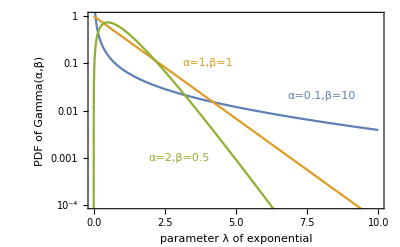

```mathematica
Show[LogPlot[{PDF[GammaDistribution[0.1,10],x],PDF[GammaDistribution[1.,1],x],PDF[GammaDistribution[2.,0.5],x]},{x,0,10}],Graphics[{cl[[1]],Text["α=0.1,β=10",{8,Log[0.02]}],cl[[2]],Text["α=1,β=1",{4,Log[0.1]}],cl[[3]],Text["α=2,β=0.5",{3,Log[0.001]}]}],PlotRange->{All,{Log[0.0001],0}},Frame->True,Axes->False,BaseStyle->12,FrameLabel->{"parameter λ of exponential","PDF of Gamma(α,β)"}]
```

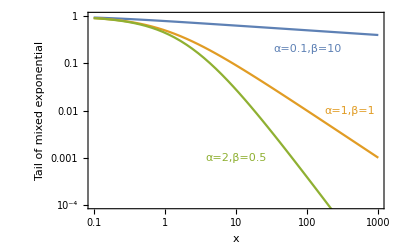

```mathematica
thplot=Show[LogLogPlot[{tail[x,0.1,10],tail[x,1.,1],tail[x,2.,0.5]},{x,0.1,1000}],Graphics[{cl[[1]],Text["α=0.1,β=10",{Log[100],Log[0.2]}],cl[[2]],Text["α=1,β=1",{Log[400],Log[0.01]}],cl[[3]],Text["α=2,β=0.5",{Log[10],Log[0.001]}]}],PlotRange->{{Log[0.1],Log[1000]},{Log[0.0001],Log[1]}},Frame->True,Axes->False,BaseStyle->12,FrameLabel->{"x","Tail of mixed exponential"}]
```

```mathematica
sample=RandomVariate[GammaDistribution[2,0.5],1000];
```

```mathematica
{Max[sample],Min[sample],Mean[sample]}
```

{5.73454,0.0308747,1.01965}

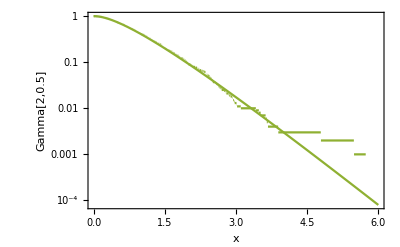

```mathematica
LogPlot[{1-CDF[EmpiricalDistribution[sample],x],1-CDF[GammaDistribution[2,0.5],x]},{x,0,6},PlotStyle->cl[[3]],FrameLabel->{"x","Tail of Gamma[2,0.5]"}]
```

```mathematica
mixs[x_]=Sum[sample[[k]]*Exp[-sample[[k]]*x],{k,1,Length[sample]}]/Length[sample];
```

```mathematica
tails[x_]=1.-Integrate[mixs[y],{y,0,x}];
```

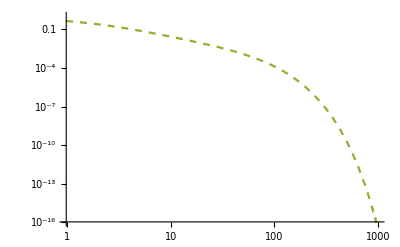

```mathematica
emplot=LogLogPlot[tails[x],{x,0,1000},PlotStyle->{cl[[3]],Dashed}]
```

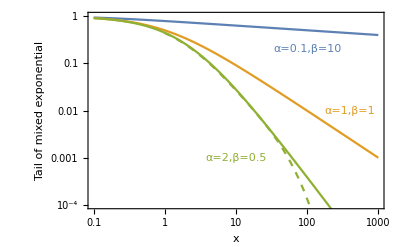

```mathematica
Show[thplot,emplot]
```

## Redistribution vs. growth

Homogeneous additive redistribution

```mathematica
nn=1000;
```

```mathematica
w0=10;time=1000000;
wealth=Table[w0,{k,1,nn}];
For[k=0,k<time,k++,r=RandomInteger[{1,nn}];If[wealth[[r]]>0,r2=RandomInteger[{1,nn}];wealth[[r]]--;wealth[[r2]]++]
]
```

```mathematica
Mean[wealth]
```

10

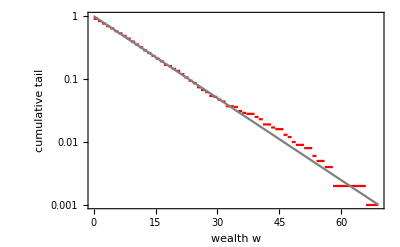

```mathematica
addi=LogPlot[1-CDF[EmpiricalDistribution[wealth],x],{x,0 ,Max[wealth]},PlotStyle->Red];
Show[addi,LogPlot[Exp[-x/Mean[wealth]],{x,0,Max[wealth]},PlotStyle->Gray],FrameLabel->{"wealth w","cumulative tail"}]
```

Homogeneous multiplicative redistribution

```mathematica
w0=10;time=1000000;
wealth=Table[w0,{k,1,nn}];
For[k=0,k<time,k++,r=RandomInteger[{1,nn}];If[wealth[[r]]>0,r2=RandomInteger[{1,nn}];d=RandomReal[]*wealth[[r]];wealth[[r]]-=d;wealth[[r2]]+=d]
]
```

```mathematica
Mean[wealth]
```

10.

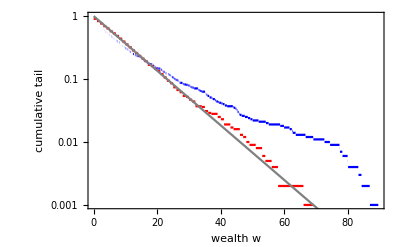

```mathematica
multi=LogPlot[1-CDF[EmpiricalDistribution[wealth],x],{x,0 ,Max[wealth]},PlotStyle->Blue];
Show[addi,multi,LogPlot[Exp[-x/Mean[wealth]],{x,0,Max[wealth]},PlotStyle->Gray],PlotRange->{All,{Log[0.001],0}},FrameLabel->{"wealth w","cumulative tail"}]
```

```mathematica
w0=10;time=1000000;
wealth=Table[w0,{k,1,nn}];
For[k=0,k<time,k++,r=RandomInteger[{1,nn}];If[wealth[[r]]>0,r2=RandomInteger[{1,nn}];d=0.5*wealth[[r]];wealth[[r]]-=d;wealth[[r2]]+=d]
]
```

```mathematica
Mean[wealth]
```

10.

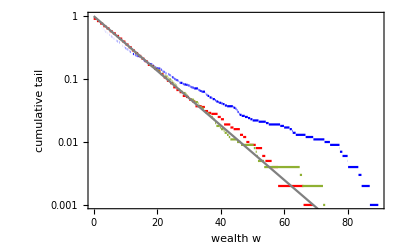

```mathematica
multifi=LogPlot[1-CDF[EmpiricalDistribution[wealth],x],{x,0 ,Max[wealth]},PlotStyle->cl[[3]]];
Show[addi,multi,multifi,LogPlot[Exp[-x/Mean[wealth]],{x,0,Max[wealth]},PlotStyle->Gray],PlotRange->{All,{Log[0.001],0}},FrameLabel->{"wealth w","cumulative tail"}]
```

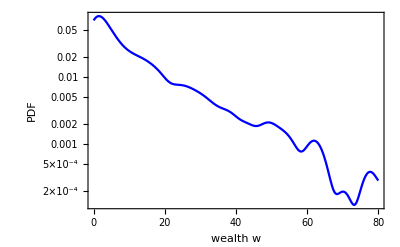

```mathematica
LogPlot[PDF[SmoothKernelDistribution[wealth],x],{x,0 ,80},PlotStyle->Blue,FrameLabel->{"wealth w","PDF"}]
```

Heterogeneous additive exchange

```mathematica
nn=200;
betas=RandomVariate[GammaDistribution[2,0.5],nn];
```

```mathematica
rates=Exp[betas];
probs=rates/Max[rates];
Min[rates]
Max[rates]
```

1.03054

31.9721

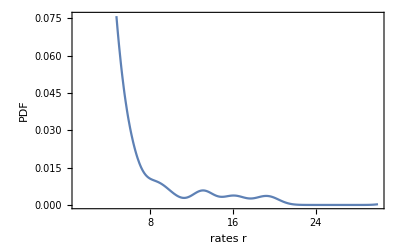

```mathematica
Plot[PDF[SmoothKernelDistribution[rates,1],x],{x,1,30},FrameLabel->{"rates r","PDF"}]
```

```mathematica
w0=10;time=2000000;
wealth=Table[w0,{k,1,nn}];
For[k=0,k<time,k++,r=RandomInteger[{1,nn}];If[wealth[[r]]>0,If[probs[[r]]>RandomReal[],r2=RandomInteger[{1,nn}];wealth[[r]]--;wealth[[r2]]++]]
]
```

```mathematica
Mean[wealth]
```

10

```mathematica
Count[wealth,0]
```

80

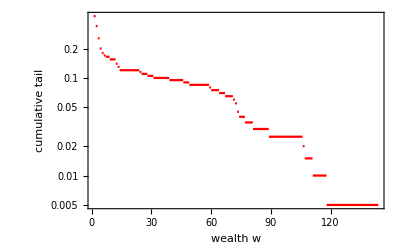

```mathematica
hetero=LogPlot[1-CDF[EmpiricalDistribution[wealth],x],{x,1,Max[wealth]},PlotRange->All,PlotStyle->Red,FrameLabel->{"wealth w","cumulative tail"}]
```

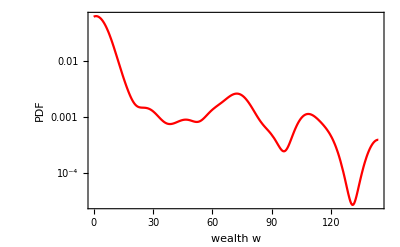

```mathematica
LogPlot[PDF[SmoothKernelDistribution[wealth,5],x],{x,0 ,Max[wealth]},PlotStyle->Red,FrameLabel->{"wealth w","PDF"}]
```

Homogeneous additive growth

```mathematica
nn=1000;w0=0;time=100000;
wealth=Table[w0,{k,1,nn}];
For[k=0,k<time,k++,r=RandomInteger[{1,nn}];wealth[[r]]++;]
```

```mathematica
Mean[wealth]
```

100

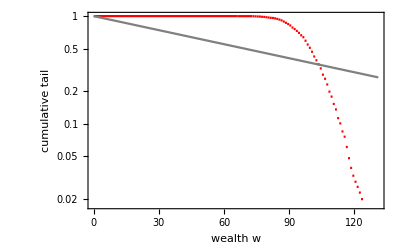

```mathematica
monoadd=LogPlot[1-CDF[EmpiricalDistribution[wealth],x],{x,0 ,Max[wealth]},PlotStyle->Red];
Show[monoadd,LogPlot[Exp[-x/Mean[wealth]],{x,0,Max[wealth]},PlotStyle->Gray],FrameLabel->{"wealth w","cumulative tail"}]
```

```mathematica
Show[dplot,DiscretePlot[PDF[PoissonDistribution[Mean[wealth]],k],{k,60,140}],FrameLabel->{"wealth w","mass function"}]
```

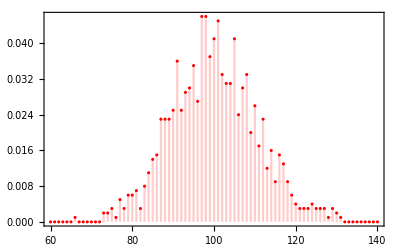

```mathematica
dplot=DiscretePlot[PDF[EmpiricalDistribution[wealth],k],{k,60,140},PlotStyle->Red]
```

Homogeneous multiplicative growth

```mathematica
nn=1000;w0=1;time=100000;
wealth=Table[w0,{k,1,nn}];money=Table[k,{k,1,nn}];
For[k=0,k<time,k++,r=RandomSample[money,1][[1]];wealth[[r]]++;money=Join[money,{r}]
]
```

```mathematica
Mean[wealth]
```

101

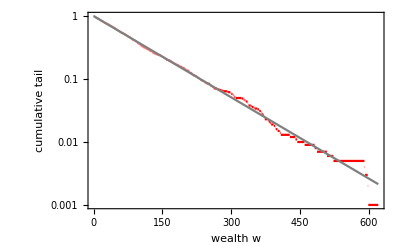

```mathematica
mono=LogPlot[1-CDF[EmpiricalDistribution[wealth],x],{x,0 ,Max[wealth]},PlotStyle->Red];
Show[mono,LogPlot[Exp[-x/Mean[wealth]],{x,0,Max[wealth]},PlotStyle->Gray],FrameLabel->{"wealth w","cumulative tail"}]
```

Heterogeneous multiplicative growth

```mathematica
nn=200;w0=1;time=100000;probs=Table[RandomReal[],{k,1,nn}];
wealth=Table[w0,{k,1,nn}];money=Table[k,{k,1,nn}];
For[k=0,k<time,k++,r=RandomSample[money,1][[1]];If[probs[[r]]>RandomReal[],wealth[[r]]++;money=Join[money,{r}]]
]
```

```mathematica
Mean[wealth]//N
```

419.21

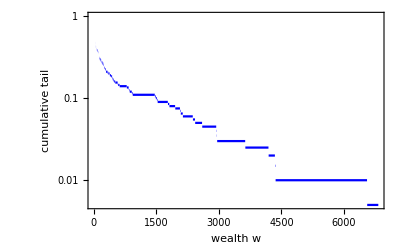

```mathematica
hetero=LogPlot[1-CDF[EmpiricalDistribution[wealth],x],{x,1,Max[wealth]},PlotStyle->Blue,FrameLabel->{"wealth w","cumulative tail"}]
```

## more stuff

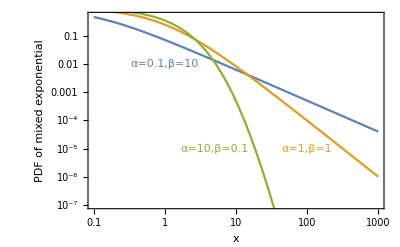

```mathematica
Show[LogLogPlot[{mix[x,0.1,10],mix[x,1.,1],mix[x,10.,0.1]},{x,0.1,1000}],Graphics[{cl[[1]],Text["α=0.1,β=10",{0,Log[0.01]}],cl[[2]],Text["α=1,β=1",{Log[100],Log[0.00001]}],cl[[3]],Text["α=10,β=0.1",{Log[5],Log[0.00001]}]}],PlotRange->{{Log[0.1],Log[1000]},{Log[0.0000001],Log[0.5]}},Frame->True,Axes->False,BaseStyle->12,FrameLabel->{"x","PDF of mixed exponential"}]
```

Inclusion process

```mathematica
pm[n_,d_,L_,S_]=FullSimplify[S!*Gamma[d*L]*Gamma[n+d]*Gamma[S-n+d*(L-1)]/Gamma[S+d*L]/n!/Gamma[d]/(S-n)!/Gamma[d*(L-1)]]
```

(S! Gamma[d L] Gamma[d+n] Gamma[d (-1+L)-n+S])/(n! (-n+S)! Gamma[d] Gamma[d (-1+L)] Gamma[d L+S])

```mathematica
0!
```

1

```mathematica
Sum[pm[k,1.5,3,1],{k,0,1}]
```

1.

```mathematica
pms[n_,L_,S_]:=(L-1.)*Product[(1.-k+S)/(L+S-(k+1)),{k,1,n}]/(L+S-1)
```

```mathematica
pms[30,2000000,3000000]
```

8.84255×10^-8

```mathematica
LL=27000000;NN=2400000000000;
```

```mathematica
??For
```

For[start,test,incr,body] executes start, then repeatedly evaluates body and incr until test fails to give True.

Attributes[For]={HoldAll,Protected}

```mathematica
pms[0,L,S]
```

(-1.+L)/(-1+L+S)

```mathematica
kk=1000000;table1=Table[0,{k,0,kk}];table1[[1]]=(LL-1.)/(LL+NN-1.);
For[k=1,k<kk,k++,table1[[k+1]]=table1[[k]]*(1.-k+NN)/(LL+NN-k-1)]
```

```mathematica
table11=Transpose[{Table[k,{k,0,kk}],1-Accumulate[table1]}];
```

```mathematica
table111=Take[table11,{100,10000,100}];
```

```mathematica
tablex=Take[table11,{10000,1000000,10000}];
```

```mathematica
pms[0,LL,NN]
```

0.0111248

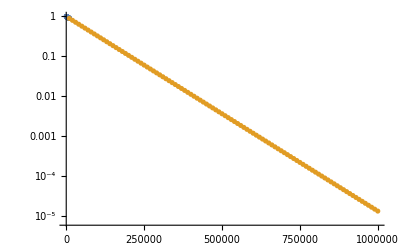

```mathematica
ListLogPlot[{table111,tablex}]
```

```mathematica
NN/LL//N
```

88888.9

```mathematica
FullSimplify[pm[n,1,L,S]]
```

((-1+L) Gamma[1+S] Gamma[-1+L-n+S])/(Gamma[L+S] Gamma[1-n+S])

```mathematica
FullSimplify[pm[3,1,L,S]]/.{L->LL,S->NN}//N
```

0.0108787

```mathematica
wtable=Table[FullSimplify[pm[k,1,L,S]]/.{L->LL,S->NN}//N,{k,0,10}]
```

$Aborted

```mathematica
NN
```

2400000000

```mathematica
LL=27000000;NN=2400000000;dd=1;
LogLogPlot[pm[n,dd,LL,NN],{n,1,10000 }]
```

$Aborted

```mathematica
RandomReal[]
```

0.855263

```mathematica
NN=88000000;kk=1000;aa=100;wtable=Table[0,{k,1,kk}];For[k=1,k<=kk,k++,rand=RandomVariate[BetaDistribution[1,aa]];wtable[[k]]=NN*rand;NN=NN*(1-rand)];
```

```mathematica
wtable
```

{3.26706×10^6,1.38414×10^6,620184.,1.17342×10^7,1.73095×10^6,1.99497×10^7,1.23456×10^6,710672.,8.82271×10^6,8.61753×10^6,312871.,5.0806×10^6,9.29477×10^6,147666.,388216.,1.46624×10^6,787450.,1.84571×10^6,812785.,130753.,132863.,551234.,1.12655×10^6,280563.,591611.,683912.,744249.,202258.,295415.,336708.,142387.,6921.23,397558.,248756.,224340.,71621.4,39678.8,648932.,172920.,676665.,88108.3,830076.,14623.7,71439.6,46663.3,348974.,3198.3,155985.,38973.2,891.621,2938.29,2660.89,112891.,39468.1,9447.85,95029.7,17311.7,46213.8,30820.3,41158.7,15473.5,10708.8,10410.2,6471.65,5797.46,898.486,6928.51,1843.36,398.467,5696.97,4365.24,2519.06,929.791,1560.75,1128.71,1043.45,200.822,416.987,1916.38,982.331,258.773,675.672,536.466,328.649,244.686,650.753,530.084,2148.16,1138.11,304.255,118.99,41.9218,434.103,126.053,44.3706,68.895,130.879,226.131,118.036,61.2468}

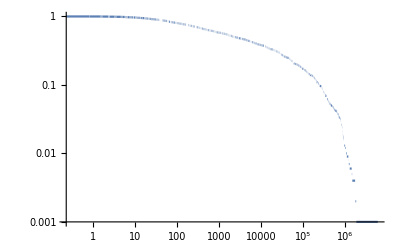

```mathematica
LogLogPlot[1-CDF[EmpiricalDistribution[wtable],x],{x,Min[wtable],Max[wtable]},PlotRange->All]
```

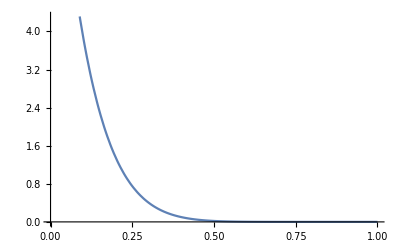

```mathematica
Plot[PDF[BetaDistribution[1,10],x],{x,0,1}]
```

```mathematica
RandomVariate[BetaDistribution[1,0.01]]
```

0.97467

```mathematica
Mean[BetaDistribution[1,a]]
```

1/(1+a)